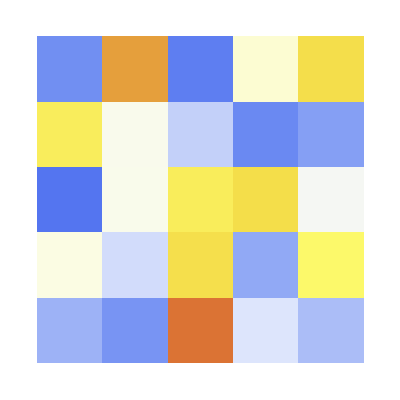
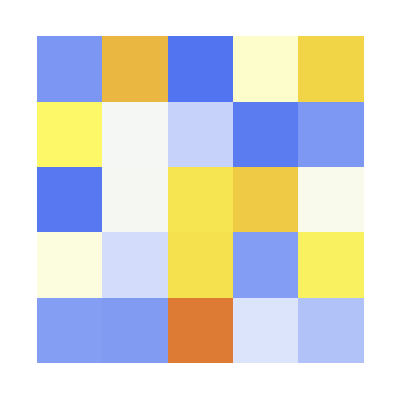
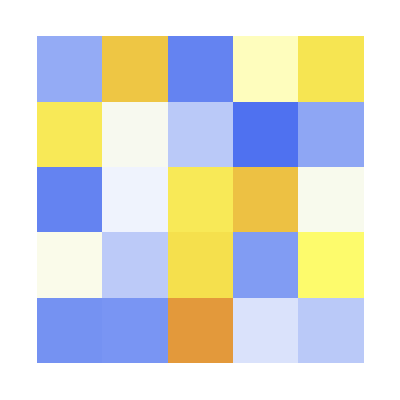
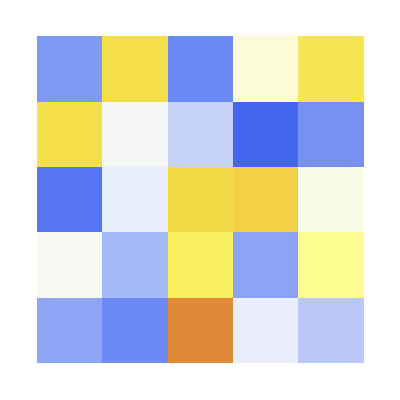
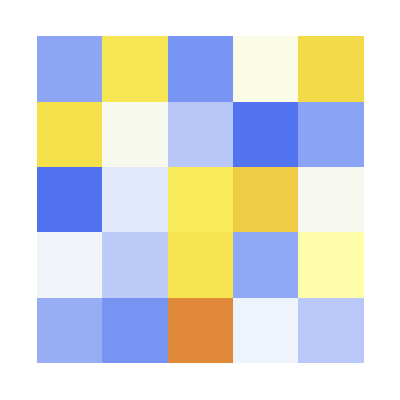
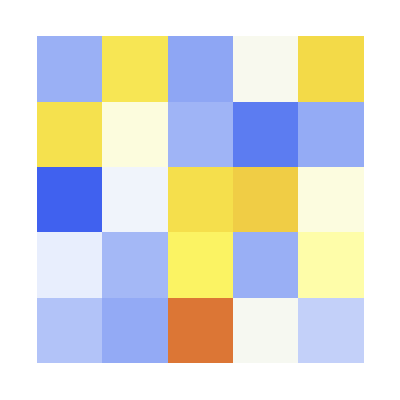
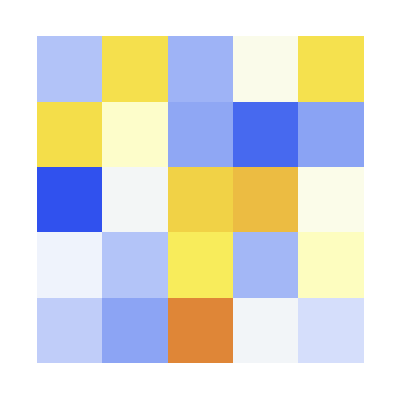
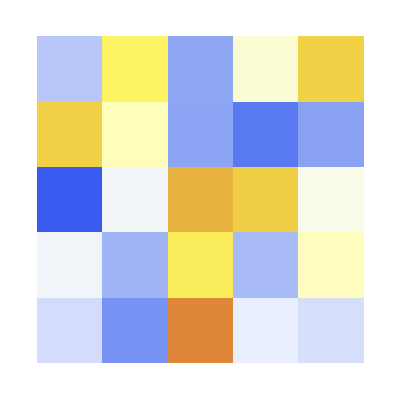

Number of steps: 10

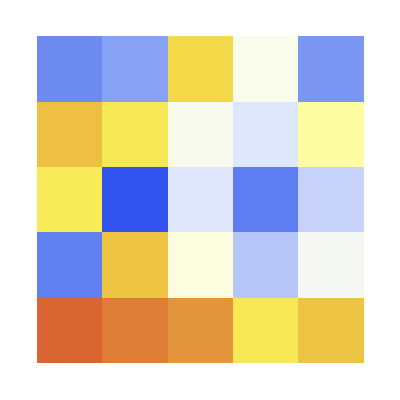
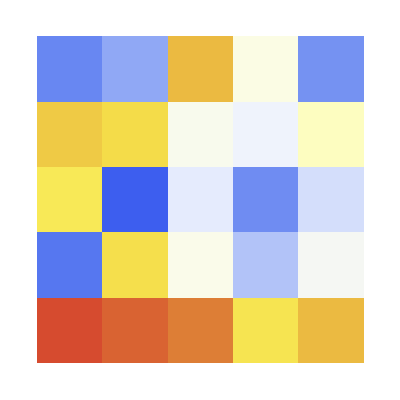
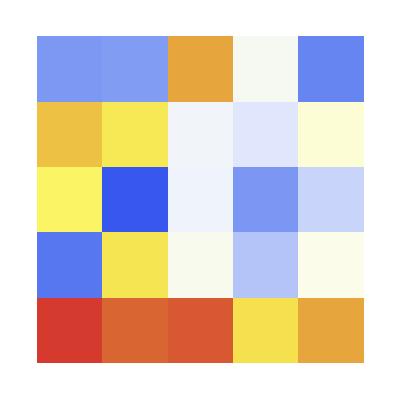
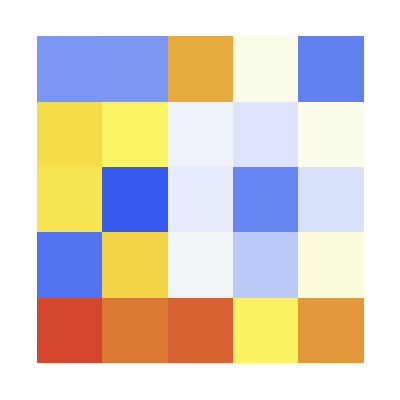
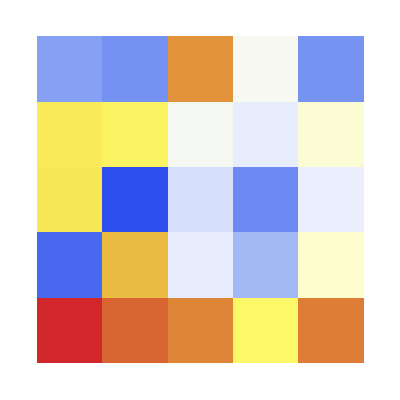
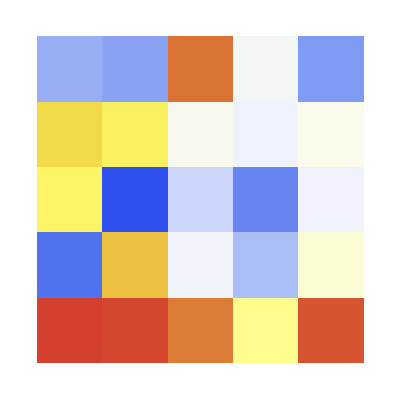
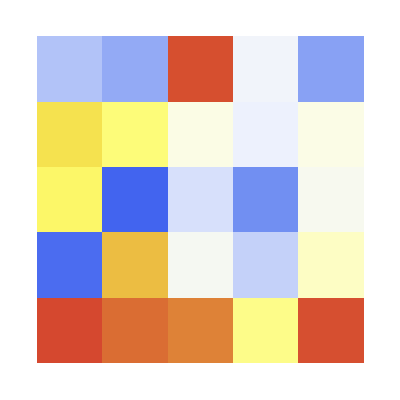
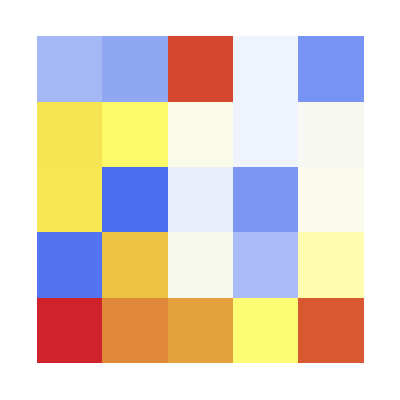

Initial gridCopy: {{0.3884395500279044, 1.7603983497297866, 1.4274030531388873, 1.1645922893871135, 0.27679682715450915}, {1.4241619525045706, 0.9675091475339398, 1.9550817545052754, 0.5876564022186935, 1.6403642029172598}, {0.06989404280274214, 1.9900751193433117, 0.410186329639205, 2., 1.170298868293352}, {1.219262191665147, 0.7802660449703197, 1.5472842775441056, 0.7896720212713111, 1.11171146601625}, {0.5353503124325205, 1.9611949740755863, 1.0950987798837606, 1.6638203874638808, 1.6768896874830959}}

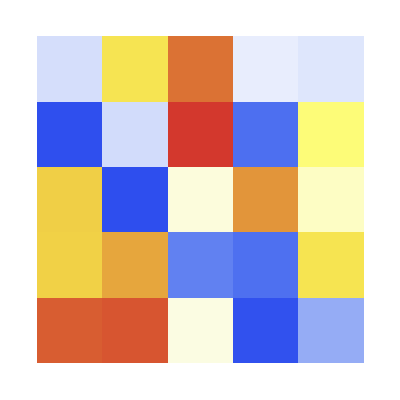
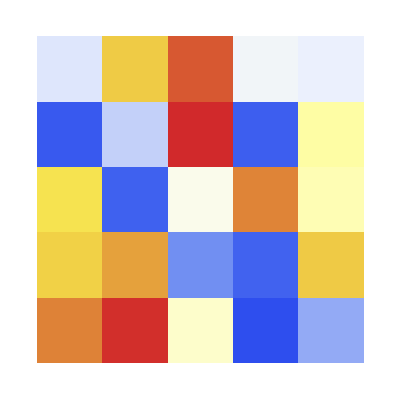
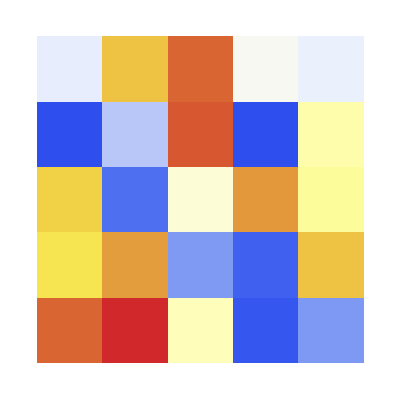
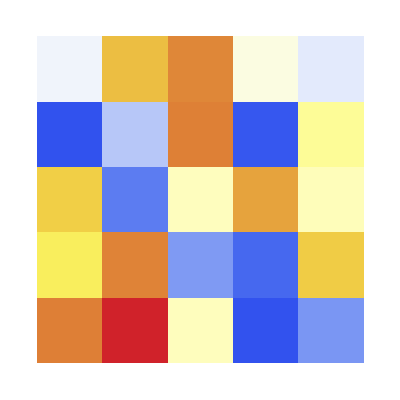
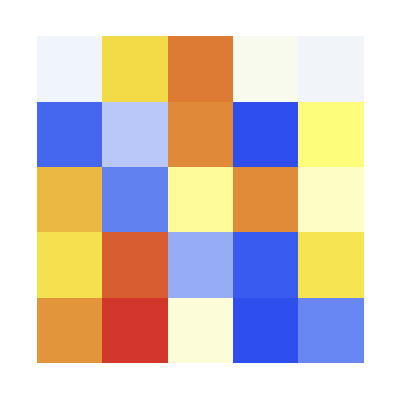
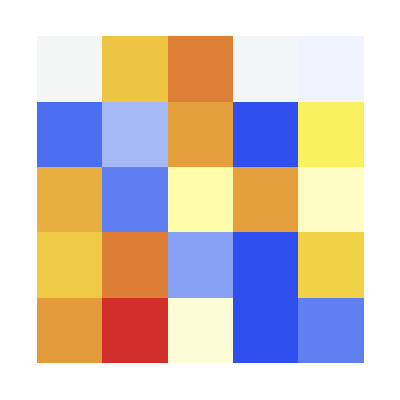
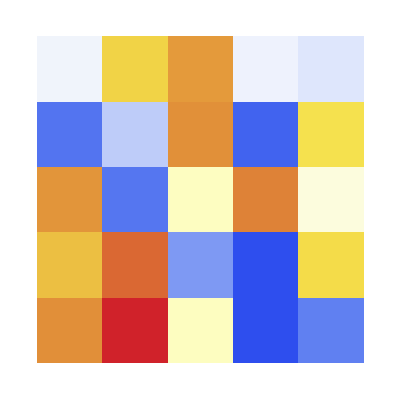
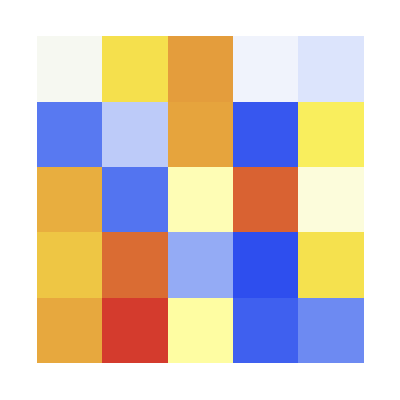

```mathematica
(*Wolfram code initiated*)(*Function to read automaton configuration from the input file*)readConfiguration[filename_]:=Module[{initialState={},rule=None,numRows=None,fileLines,line},(*Try to read the file and process each line*)fileLines=Check[Import[filename,"Lines"],Print["Error: The file '",filename,"' was not found."];Return[]];
(*Process lines to extract parameters*)Do[line=StringTrim[fileLines[[i]]];
If[StringStartsQ[line,"initial_state:"],initialState=ToExpression[StringSplit[StringTrim[StringSplit[line,":"][[2]]],","]];];
If[StringStartsQ[line,"rule:"],rule=ToExpression[StringTrim[StringSplit[line,":"][[2]]]];];
If[StringStartsQ[line,"rows:"],numRows=ToExpression[StringTrim[StringSplit[line,":"][[2]]]];];,{i,Length[fileLines]}];
(*Check if rule and numRows are defined*)If[rule===None||numRows===None,Print["Error: Missing rule or rows in the configuration file."];
Return[]];
{initialState,rule,numRows}]

(*Update grid function with analog growth and decay*)
updateGrid[grid_,baseGrowthProb_,baseDecayProb_]:=Module[{newGrid=grid,size=Length[grid],growthProb,decayProb},For[i=1,i<=size,i++,For[j=1,j<=size,j++,growthProb=baseGrowthProb*RandomReal[{0.8,1.2}];(*Add variability to growth*)decayProb=baseDecayProb*RandomReal[{0.8,1.2}];(*Add variability to decay*)If[grid[[i,j]]>0,(*If not empty*)If[grid[[i,j]]<1.0,(*If a sapling,grow towards 1.0*)newGrid[[i,j]]=newGrid[[i,j]]+growthProb*(1.0-grid[[i,j]]),(*If a stunted tree,decay towards 0*)newGrid[[i,j]]=newGrid[[i,j]]-decayProb*grid[[i,j]]];
(*Clamp values between 0 and 2 for visualization*)newGrid[[i,j]]=Max[0.0,Min[newGrid[[i,j]],2.0]];]]];
newGrid]

gridCopy=RandomReal[{0,2},{5,5}];
Table[gridCopy=Map[Clip[#,{0,2}]&,gridCopy+RandomReal[{-0.1,0.1},{5,5}]];
ArrayPlot[gridCopy,ColorFunction->"TemperatureMap",PlotRange->{0,2}],{step,1,10}]

(*Initialize the grid with continuous values based on sapling_prob*)
initializeGrid[size_,saplingProb_]:=Table[RandomReal[]*saplingProb,{size},{size}]

numSteps=10;  (*or another suitable integer*)

grid=RandomReal[{0,2},{5,5}];  (*A 5x5 grid with random values between 0 and 2*)

updateGrid[grid_,saplingGrowthProb_,treeDecayProb_]:=Map[Clip[#+RandomReal[{-0.1,0.1}],{0,2}]&,grid,{2}];

gridCopy=RandomReal[{0,2},{5,5}];
Table[gridCopy=Map[Clip[#,{0,2}]&,gridCopy+RandomReal[{-0.1,0.1},{5,5}]];
ArrayPlot[gridCopy,ColorFunction->"TemperatureMap",PlotRange->{0,2}],{step,1,10}]

Print["Number of steps: ",numSteps];
(*Initialize variables*)numSteps=10;
gridSize=5;
grid=RandomReal[{0,2},{gridSize,gridSize}];

gridCopy=RandomReal[{0,2},{5,5}];
Table[gridCopy=Map[Clip[#,{0,2}]&,gridCopy+RandomReal[{-0.1,0.1},{5,5}]];
ArrayPlot[gridCopy,ColorFunction->"TemperatureMap",PlotRange->{0,2}],{step,1,10}]

(*Example update function*)
updateGrid[grid_,saplingGrowthProb_,treeDecayProb_]:=Map[Clip[#+RandomReal[{-0.1,0.1}],{0,2}]&,grid,{2}];

gridCopy=RandomReal[{0,2},{5,5}];
Table[gridCopy=Map[Clip[#,{0,2}]&,gridCopy+RandomReal[{-0.1,0.1},{5,5}]];
ArrayPlot[gridCopy,ColorFunction->"TemperatureMap",PlotRange->{0,2}],{step,1,10}]

(*Main loop*)
Do[grid=updateGrid[grid,0.1,0.1];(*Replace with your probabilities*)ArrayPlot[grid,ColorFunction->"Rainbow",PlotRange->{0,2},PlotLabel->"Sparse Forest of Stunted Trees - Step "<>ToString[step],ColorFunctionScaling->False];
Pause[0.1];,{step,1,numSteps}]

numSteps=10; (*or another appropriate integer*)

Print["Initial gridCopy: ",ToString[gridCopy,InputForm]];

(*Run the simulation*)
Do[(*Update the grid based on your update rules*)grid=updateGrid[grid,saplingGrowthProb,treeDecayProb];
(*Display the grid using a valid color function*)ArrayPlot[grid,ColorFunction->"Rainbow",PlotRange->{0,2},PlotLabel->StringJoin["Sparse Forest of Stunted Trees - Step ",ToString[step]],ColorFunctionScaling->False];
(*Pause to view the plot*)Pause[0.1];,{step,1,numSteps}]

gridCopy=RandomReal[{0,2},{5,5}];
Table[gridCopy=Map[Clip[#,{0,2}]&,gridCopy+RandomReal[{-0.1,0.1},{5,5}]];
ArrayPlot[gridCopy,ColorFunction->"TemperatureMap",PlotRange->{0,2}],{step,1,10}]

numSteps=10;
runSimulation[gridSize_,saplingProb_,growthProb_,decayProb_,numSteps_]:=
Module[{gridSize,numSteps},gridSize]=5;
grid=updateGrid[grid,growthProb,decayProb];
Pause[0.1];,{step,numSteps};

gridCopy=RandomReal[{0,2},{5,5}];
Table[gridCopy=Map[Clip[#,{0,2}]&,gridCopy+RandomReal[{-0.1,0.1},{5,5}]];
ArrayPlot[gridCopy,ColorFunction->"TemperatureMap",PlotRange->{0,2}],{step,1,10}]

(*Constants and parameters for the simulation*)
gridSize=250; (*Size of the grid*)
saplingGrowthProb=0.025; (*Probability of sapling growing into a stunted tree*)
treeDecayProb=0.35; (*Probability of stunted tree decaying back to empty*)
initialSaplingProb=0.4; (*Initial probability of each cell starting as a sapling*)
numSteps=250; (*Number of steps to run the CA*)

(*Set the working directory to Desktop*)SetDirectory["C:\\Users\\User\\Desktop"];

gridCopy=RandomReal[{0,2},{5,5}];
Table[gridCopy=Map[Clip[#,{0,2}]&,gridCopy+RandomReal[{-0.1,0.1},{5,5}]];
ArrayPlot[gridCopy,ColorFunction->"TemperatureMap",PlotRange->{0,2}],{step,1,10}]

#(*Initialize the grid and step counter*)gridSize=5;
# numSteps=10;

numSteps=10;  (*or any number of steps you desire*)

(*Initialize grid and ensure it's a 2D list*)gridSize=5;
ggridCopy=RandomReal[{0,2},{5,5}];
Table[gridCopy=Map[Clip[#,{0,2}]&,gridCopy+RandomReal[{-0.1,0.1},{5,5}]];
ArrayPlot[gridCopy,ColorFunction->"TemperatureMap",PlotRange->{0,2}],{step,1,10}]

(*Check the dimensions to confirm it's a 2D list*)
Print["Dimensions of gridCopy before manipulation: ",Dimensions[gridCopy]];

(*Manipulate the grid while keeping its structure*)
gridCopy=Map[Clip[#+RandomReal[{-0.1,0.1}],{0,2}]&,gridCopy,{2}];

(*Check again after manipulation*)
Print["Dimensions of gridCopy after manipulation: ",Dimensions[gridCopy]];

DynamicModule[{grid=RandomReal[{0,2},{5,5}],step=0},Dynamic[ArrayPlot[grid,ColorFunction->"TemperatureMap",PlotRange->{0,2}]]]

gridCopy=RandomReal[{0,2},{5,5}];
Table[gridCopy=Map[Clip[#,{0,2}]&,gridCopy+RandomReal[{-0.1,0.1},{5,5}]];
ArrayPlot[gridCopy,ColorFunction->"TemperatureMap",PlotRange->{0,2}],{step,1,10}]

ArrayPlot[{{0.1,0.2},{0.3,0.4}},ColorFunction->"TemperatureMap",PlotRange->{0,2}]

(*Use ArrayPlot if gridCopy is correctly formatted*)
If[MatrixQ[gridCopy],Print["gridCopy is a 2D list with dimensions: ",Dimensions[gridCopy]],Print["Error: gridCopy is not a 2D list"]];

gridCopy=RandomReal[{0,2},{5,5}];
Table[gridCopy=Map[Clip[#,{0,2}]&,gridCopy+RandomReal[{-0.1,0.1},{5,5}]];
ArrayPlot[gridCopy,ColorFunction->"TemperatureMap",PlotRange->{0,2}],{step,1,10}]

$DisplayFunction=Identity;  (*Ensure graphics are displayed*)

ClearAll["Global`*"];
Quit[]
(*Wolfram code completed*)
```

```mathematica
Null
```